# Lab 3

## Related Rates and Tangent Line Approximations

John Erickson, IIT

## Introduction

The topics of related rates and tangent line approximations are sections 2.8 and 2.9 of your text.

## Related Rates

The idea of related rates is quite simple if quantites are related, which means one quantity depends on another quantity through some function (which is perhaps defined implicitly), then if you change the first quantity, the second quantity should change. Moreover the rate at which you change the first quantity should somehow be connected to the rate at which the second quantity changes. The easiest way to get a handle on these ideas is through some concrete examples. We will consider to classic problems.

### The Sliding Ladder Problem

A ladder 10m long is leaning against the wall and the bottom starts to slide at a rate of 1 m/s. How fast is the top of the ladder sliding down when the the bottom of the ladder is 6m from the wall? We did this problem in class and you should be able to do it analytically. Now play with the manipulate below to answer the questions which below.

```mathematica
Manipulate[Show[If[locus,ParametricPlot[{(√(100-t^2))/2,t/2},{t,0,10},PlotStyle-> Dashed],Graphics[{PointSize[.02],Point[{x,0}]}]], Graphics[{Red,PointSize[.02],Point[{x/2,(√(100-x^2))/2}],Black,PointSize[.02],Point[{x,0}],Point[{0,√(100-x^2)}],Line[{{0,√(100-x^2)},{x,0}}]}]
,Axes-> True, PlotRange-> 10],{{x,0,"dist"},0,10},{{locus,False},{True,False}}]
```

### Light Beam Moving in a Circle Problem

One example that comes to mind is something that we can all relate to. Have you ever used a flashlight to look for something and panned it back and forth along the floor, a wall, or even low hanging fog. If you have, you my have noticed, that at the “ends” of your panning motion the light beam appears to have sped up and is moving quite fast. We can abstract this situation in the Manipulate below in which a point is moving along a circular path at a uniform speed and we look at the shadow of the point along a line under the circle cast by a light located at the center at the circle.

```mathematica
Manipulate[ParametricPlot[{Cos[t],Sin[t]+1},{t,0,2π},PlotRange-> {{-10,10},{-1,2}},Epilog-> {Point[{0,1}],{Green,PointSize[.01],Point[{Cos[s],Sin[s]+1}]},Line[{{0,1},{-Cot[s],0}}],Red,PointSize[.01],Point[{-Cot[s],0}]},ImageSize->Large],{s,-π+.1,-.1}]
```

### The Cone Problem

If you have ever filled up a jug with a tapered top, you have experienced related rates. As the water heads towards the tapered top, the height of the water increases faster and faster and you can even hear the “wooshing” sound this created.

```mathematica
Manipulate[ContourPlot3D[{z==10-(1000-3/π t)^(1/3),x^2+y^2==(10-z)^2},{x,-10,10},{y,-10,10},{z,0,10},Mesh-> False,ContourStyle-> Opacity[.4],Boxed-> False, Axes-> False,PerformanceGoal->"Quality"],{t,0,1000 π/3} ]
```

## The Tangent Line as a best linear approximation

The derivative is defined in terms of a limit and determines the slope of the tangent line to a curve. It turns out however that resulting tangent line can also be thought of as the best linear approximation to the curve near the point in question. The manipulate below explores this connection.

```mathematica
Manipulate[Module[{sol,x},sol=Solve[x^2==m(x-a)+a^2,x];point={x,x^2}/.sol;Show[Plot[{x^2,m(x-a)+a^2},{x,a-δ,a+δ} ,PlotRange-> {{-14,14},{-120,200}},AspectRatio-> 1,PlotStyle->{{Thickness[.005],Blue},{Thickness[.005], Red}},AxesLabel-> {"x","y"},Epilog->{ Green,PointSize[Medium],Point[point]},PlotLabel-> TraditionalForm["deriv = "<>ToString[2a]<>"  secant slope = "<>ToString[m]<>"   norm = "<>ToString[(NIntegrate[Abs[x^2-m(x-a)-a^2]^p,{x,a-δ,a+δ}]^(1/p))/(2δ)]],Filling->{1->{2}}],

Plot[{x^2,m(x-a)+a^2},{x,-13,13} ,PlotRange-> {{-14,14},{-120,200}},AspectRatio-> 1,PlotStyle->{{Thickness[.005],Blue},{Thickness[.005], Red}}]]],{{a,5},-9,9},{{m,0},-20,20},{δ,4,.01,-.01},{{p,2},1,10}]
```

## Problems

### Related Rates Problems

#### Sliding Ladder Problems

You can call the height of the edge of the ladder leaning against the wall y and the distance from of the bottom of the ladder from the wall x in what follows.

1.Where does it appear that the edge of the ladder leaning against the wall is falling fastest? Now explain why this makes sense from the math we have already worked out. You will need to use the formulas we derived already in class for this and explain why what we are seeing is consistent with that formula.

```mathematica
Dt[x^2+y^2==10^2,t]
```

2 x Dt[x,t]+2 y Dt[y,t]==0

```mathematica
Solve[2 x Dt[x,t]+2 y Dt[y,t]==0, Dt[y,t]]
```

{{Dt[y,t]→-(x Dt[x,t])/y}}

It falls fastest at the bottom: the speed of the falling approaches infinity as y approaches 0.

2.This is interesting. We have focused on the top and the bottom of the ladder, but suppose your friend was on the ladder right in the middle and she/he was holding a light. If it were dark outside, what path would you see traced out by her/his light? It is fairly easy to guess the answer since I have provided you with a nice little button for this. Now prove your answer.

A quadrant of a circle.

When the ladder starts to slide the top is moving vertically very slowly, while the bottom is moving very quickly. Conversely, when the ladder approaches the end of its motion, the top (now the left) of the ladder is moving very quickly, but the bottom (now the right) is moving very slowly. These two speeds are in ratio, and cancel eachother out; this means that the midpoint *starts out* moving nearly directly horizontally (as the bottom of the ladder moves out from the way, dragging the midpoint with it), and describes a clean circle, with it touching y=-x tangentially as the ladder completes the first half of its’ movement, and then is moving almost directly vertically (approaching the vertical tangent y=C) as  the top of the ladder completes its motion towards the ground.

#### Circular Light Beam Problem

In what follows, note that we are measuring our angle as usual with our initial side in the postive x direction, but our unit circle has now been shifted up to have center (0,1).

3. Where does the red point seem to be moving fastest? Where does it appear to be moving slowest?

Fastest near the ends (when the slope of the line approaches horizontal), and slowest near the center (where the slope of the line approaches vertical.)

4. The red point actually intersects the x-axis at the point (-cot t,0) where t is the angle. Can you prove this using elementary trig? If you were expecting tan(t) remember, we are measuring angles using our “initial ray” as determined by the points (0,1) to (1,1).

```mathematica
Solve[Tan[t]x+1==0,x]
```

{{x→-Cot[t]}}

5. Now find the velocity the of the red point by taking the derivative with respect to t. You don’t need Mathematica for this, and you should in fact even remember the answer, but it’s nice to see that it’s so easy to do this.

```mathematica
Dt[-Cot[t],t]
```

Csc[t]^2

6. Now plot the function above to see where the velocity gets big, in fact, potentially approaching infinity, and also where it gets smallest. Verify that this makes sense.

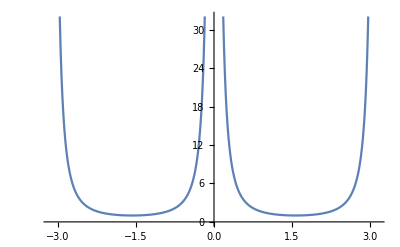

```mathematica
Plot[Csc[t]^2, {t, -π, π}]
```

The velocity grows unbounded as t approaches π or 0.

7. Now find the where the velocity is smallest, by finding a critical point of the velocity (in other words, when is the acceleration equal to zero) ANALYTICALLY. You will find the Solve command useful here.

```mathematica
Reduce[D[Csc[t]^2, t] == 0 && -π≤t≤0, t]
```

t==-π/2

#### Cone Problem

8. If we assume that the cone above has a height and radius of 10m, and it is being filled up at a constant rate of 1 m^3/s, then find the formula for ⅆh/ⅆt and explain how this formula relates (no pun intended) to what you observed.

```mathematica
V[h_,r_]:=1/3 π r^2 h
```

```mathematica
10/10==r/h; 1 == r/h; h==r
```

```mathematica
V2[h_]:=V[h,h]
```

```mathematica
V2[h]
```

(h^3 π)/3

```mathematica
Vt[h_]:=Dt[V2[h]]
```

```mathematica
Vt[h]
```

h^2 π Dt[h]

```mathematica
Solve[Vt[h]==1, Dt[h]]
```

{{Dt[h]→1/(h^2 π)}}

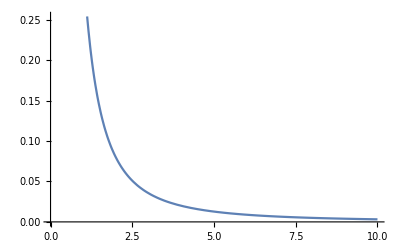

```mathematica
Plot[1/(h^2 π), {h, 0, 10}]
```

As the remaining space decreases, the rate at which the volume is increasing, increases. This accounts for the ‘whooshing’ sound, as the air is being pushed out of the container at higher and higher speeds (and thus higher and higher pressures), thus changing the tonality of the resultant sound-of-rushing-air.

#### The tangent line as a linear approximation problem

9. Using the default values of a=5, δ=4, and p=2, what is the minimum value of “norm” as a function of m, the secant slope, and for what value of m  was this minimum achieved? What does this illustrate? Obviously, we haven’t fully explained what the “norm” is, but even an intuitive understanding should be enough to get the point.

```mathematica
2.52982
```

This is showing that as a secant-line approaches becoming the singular tangent-line, the ‘size’ of the error (the area between the tangent and the actual curve) minimizes; with the tangent-line itself being a global minimum on the size-of-the-error.